```mathematica
a+1
```

1+a

```mathematica
?Sin
```

Sin[z] gives the sine of z.

```mathematica
(* My comment *)
a+1
```

1+a

Here is my first text cell.

```mathematica
a+b
```

a+b

Aha, this is the result.

```mathematica
a=5
```

5

```mathematica
a
```

5

```mathematica
b=a
```

5

```mathematica
b
```

5

```mathematica
a=5
```

5

```mathematica
a
```

5

```mathematica
c:=a
```

```mathematica
c
```

5

```mathematica
a=10
```

10

```mathematica
c
```

10

```mathematica
Clear[a,b,c]
```

```mathematica
a
```

a

```mathematica
b
```

b

```mathematica
c
```

c

```mathematica
a=12
```

12

```mathematica
a
```

```mathematica
a+b
```

```mathematica
a b
```

12 b

```mathematica
8*9
```

72

```mathematica
8 9
```

72

```mathematica
x^a
```

x^12

```mathematica
x^a
```

x^12

```mathematica
x^a
```

x^12

```mathematica
(a^8)^(1/4)
```

144

```mathematica
ⅇ^x
```

ⅇ^x

```mathematica
α
```

```mathematica
𝔼
```

```mathematica
𝒜
```

```mathematica
ℬ
```

```mathematica
Clear[a]
```

```mathematica
Expand[a(b+c)-a(e-f),]
```

a b+a c-a e+a f

```mathematica
a(b+c)-a(e-f)//Expand
```

a b+a c-a e+a f

```mathematica
expr2=a b+(x-z)b+(e+f-g)a
```

a b+a (e+f-g)+b (x-z)

```mathematica
Collect[expr2,{a}]
```

a (b+e+f-g)+b (x-z)

```mathematica
Collect[expr2,{a,b}]
```

a (b+e+f-g)+b (x-z)

```mathematica
Collect[expr2,{b}]
```

a (e+f-g)+b (a+x-z)

```mathematica
myList1
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
myList1[[{1,5,6}]]
```

{1,5,6}

```mathematica
myNestedList1
myNestedList1[[1]]
```

{{a,b},{c,d}}

{a,b}

```mathematica
myNestedList1[[1,2]]
```

b

```mathematica
myList1
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
myList1[[-3]]
```

8

```mathematica
myList1[[-6;;-4]]
```

{5,6,7}

```mathematica
myList1
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Position[myList1,6]
```

{{6}}

```mathematica
myNestedList2
```

{{{a,1},{b,1},{c,1},{d,1},{e,1}},{{a,2},{b,2},{c,2},{d,2},{e,2}},{{a,3},{b,3},{c,3},{d,3},{e,3}},{{a,4},{b,4},{c,4},{d,4},{e,4}},{{a,5},{b,5},{c,5},{d,5},{e,5}}}

```mathematica
Position[myNestedList2,{d,2}]
```

{{2,4}}

```mathematica
myNestedList2[[2,4]]
```

{d,2}

```mathematica
myNestedList1
```

{{a,b},{c,d}}

```mathematica
Flatten[myNestedList1]
```

{a,b,c,d}

```mathematica
?Flatten
```

Flatten[list] flattens out nested lists. 
Flatten[list,n] flattens to level n. 
Flatten[list,n,h] flattens subexpressions with head h. 
Flatten[list,{{s_11,s_12,…},{s_21,s_22,…},…}] flattens list by combining all levels s_ij to make each level i in the result.

```mathematica
myList1
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
myList2
```

{a,b,c,d,e,f,g,h,i,j}

```mathematica
Riffle[myList1,myList2]
```

{1,a,2,b,3,c,4,d,5,e,6,f,7,g,8,h,9,i,10,j}

```mathematica
Partition[Riffle[myList1,myList2],2]
```

{{1,a},{2,b},{3,c},{4,d},{5,e},{6,f},{7,g},{8,h},{9,i},{10,j}}

```mathematica
?Partition
```

Partition[list,n] partitions list into nonoverlapping sublists of length n. 
Partition[list,n,d] generates sublists with offset d. 
Partition[list,{n_1,n_2,…}] partitions a nested list into blocks of size n_1×n_2×… .
Partition[list,{n_1,n_2,…},{d_1,d_2,…}] uses offset d_i at level i in list. 
Partition[list,n,d,{k_L,k_R}] specifies that the first element of list should appear at position k_L in the first sublist, and the last element of list should appear at or after position k_R in the last sublist. If additional elements are needed, Partition fills them in by treating list as cyclic. 
Partition[list,n,d,{k_L,k_R},x] pads if necessary by repeating the element x. 
Partition[list,n,d,{k_L,k_R},{x_1,x_2,…}] pads if necessary by cyclically repeating the elements x_i. 
Partition[list,n,d,{k_L,k_R},{}] uses no padding, and so can yield sublists of different lengths. 
Partition[list,nlist,dlist,{klist_L,klist_R},padlist] specifies alignments and padding in a nested list.

```mathematica
Join[myList1,myList2]
```

{1,2,3,4,5,6,7,8,9,10,a,b,c,d,e,f,g,h,i,j}

```mathematica
myList3
```

{20,4,10,2,4,5}

```mathematica
Sort[myList3]
```

{2,4,4,5,10,20}

```mathematica
myList3
```

{20,4,10,2,4,5}

```mathematica
Split[myList3]
```

{{20},{4},{10},{2},{4},{5}}

```mathematica
Split[Sort[myList3]]
```

{{2},{4,4},{5},{10},{20}}

```mathematica
b
```

a

```mathematica
b/.myRule1
```

5

```mathematica
Sin[x]
```

Sin[x]

```mathematica
Sin[2π]
```

0

```mathematica
Sin[x]/.{x->2π}
```

0

```mathematica
myFunc1[1,4,3]
```

7/3

```mathematica
b
```

a

```mathematica
myFunc2[x]
```

x^2 α+x β+γ

```mathematica
myFunc2[y]
```

y^2 α+y β+γ

```mathematica
myFunc2[x]/.{α->1,β->2,γ->4}
```

4+2 x+x^2



```mathematica
Plot[Sin[x],{x,0,2π}]
```

```mathematica
?myFunc1
```

Global`myFunc1

myFunc1[a_,b_,c_]:=a+b/c

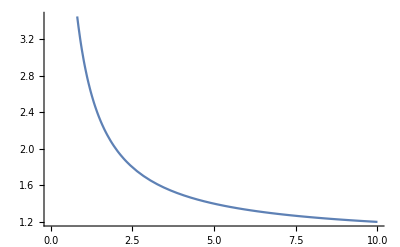

```mathematica
Plot[myFunc1[1,2,c],{c,0,10}]
```